## Introduction

π is indicated by Pi

nearly all operations in  Mathematica returns after manipulating and do not change the actual value, so we have to take it as return we we want to change.

Mathematica is case sensitive language

It uses camel Notation for function names

```mathematica
Pi
```

π

finding numerical value of something we can use N[<value>] or N[<value>,int_precision_digits]

N[Pi]

3.14159

```mathematica
N[π,20]
```

3.1415926535897932385

Mathematica is case sensitive language so,

```mathematica
2*pi
```

2 pi

which is not 2*Pi

```mathematica
Round[21.8] //round to nearest integer
```

22

```mathematica
Round[21.6,0.5]//round to nearest multipleof 0.5
```

21.5

## Adding comments and documentation

for comment we can use (* and *) in mathematica

when we define a function we may add some documentation to it so that any one can easily able to understand the basic functionality of that funciton.

for getting help about any method we can use ?<function_name>

```mathematica
ex -for Plot function
```

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.

```mathematica
power[a_,exp_]:=a^exp;
```

for adding help or documentation we need to use usage keyword

```mathematica
power::usage=" gives a to the power exp ";
```

```mathematica
?power
```

gives a to the power exp

## ->{654, 659}, WindowMargins->{{Automatic, 21}, {Automatic, 0}}, PrintingCopies->1, PrintingPageRange->{32000,

one of the most ofter problem in mathematica is that the variables and function do not go away if we create a new notebook they remain in RAM.

so if i define a variable and create a new notebook then i will be able to find it there as well, it might cause some problem so Clear[] if some problem occurs.

## Suppressing output in Mathematica

generally mathematica evaluates each and every line and show output for it

if we do not want output for some line we can suppress output using semicolon(;), this is same as matlab

we will do it when we wanted mathematica to execute that line but do not show us output of that.(for execution shift+enter)

```mathematica
var1={1,2,3} (* output of this line will be shown *)
```

{1,2,3}

```mathematica
var2={1,2,3}; (* output of this line will not be shown *)
```

Mathematical Operators

+ and - for add and subtract

* or space for multiplication so (a b) is same as (a*b)

/ for division and ^ for power

## Mathematical Functions

Mod[x,y] return reminder

Mod[m,n] gives the remainder on division of m by n. 
Mod[m,n,d] uses an offset d.

Quotient[x,y] returns quotient of division

N[x] returns numerical represenation of fraction or other expression

N[x,n] return numerical value upto n digits after decimal

BaseForm[x,b] convert base 10 number x in base b

Factor[poly] factorise polynomial

Factor[poly] factors a polynomial over the integers. 
Factor[poly,Modulus→p] factors a polynomial modulo a prime p. 
Factor[poly,Extension→{a_1,a_2,…}] factors a polynomial allowing coefficients that are rational combinations of the algebraic numbers a_i.

### Prime Number functions

Prime[n] gives the n^th prime number.

NextPrime[n] gives the next prime above n.
NextPrime[n,k] gives the k^th prime above n.

PrimePi[x] gives the number of primes π(x) less than or equal to x.

```mathematica
PrimePi[10](* no of primes up to 10 *)
```

4

```mathematica
16 Pi
```

16 π

```mathematica
N[16Pi]
```

50.2655

```mathematica
BaseForm[20,3]
```

202_3

```mathematica
BaseForm[20,5]
```

40_5

```mathematica
Factor[1+x ^3]
```

(1+x) (1-x+x^2)

Series[] function expands a function

Series[f,{x,x_0,n}] generates a power series expansion for f about the point x=x_0 to order (x-x_0)^n. 
Series[f,{x,x_0,n_x},{y,y_0,n_y},…] successively finds series expansions with respect to x, then y, etc.

```mathematica
Series[Exp[x],{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

normal removes last term

```mathematica
Normal[Series[Exp[x],{x,0,10}]] (* this is expansion for e^x from x=0 to 10 *)
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800

```mathematica
Normal[Series[Sin[x],{x,0,10}]]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

## Referring to previous calculations

one of the most important feature of mathematica is that it can refer to previously done calculations and this is the reason why every calculation(input as well as output) have a number associated with it. ex- In[11] and Out[11]

if we wanted to refer to last previous output then use % sign

```mathematica
%  //which as the last output
```

```mathematica
50.26548245743669
%11
```

```mathematica
50.26548245743669
```

16 π

to work with output no 11 we can use %11 or Out[11], this will acts as variable

```mathematica
%11
```

```mathematica
16 π
```

```mathematica
Out[11]
```

16 π

## Using variables

rules for creating variables are same as C

_(underscore ) can ‘t be used here, because we use them in function definitions for variables

rules of variables applied to all identifiers(function names etc.)

```mathematica
2=20
```

Set::setraw: Cannot assign to raw object 2.

20

```mathematica
a=20
```

20

```mathematica
a*20/3
```

400/3

```mathematica
_a=20
```

Set::write: Tag Integer in Blank[20] is Protected.

20

for clearing a variable we can use Clear[var_name] method.

## Importing and Exporting data from Files

Import[“<file_path>”] is the function which is used to import data

file_path could be absolute path, relative path or url

file could be text , csv(stylesheet) , gif or any type

```mathematica
var=Import["C:\\Users\\ashish_patel\\Desktop\\info.txt"]
```

10
20
30
40
50
60
70

for showing data in table form we can use TableForm[data_list] function

```mathematica
TableForm[var]
```

10
20
30
40
50
60
70

similarly for exporting we use Export[“file_path”,variable_name].

if file specified in file_path not available file will be created.

```mathematica
Export["C:\\Users\\ashish_patel\\Desktop\\infoexport.txt",var]
```

C:\Users\ashish_patel\Desktop\infoexport.txt

## Built-in Functions

Sqrt[x] find square root

IntegerPart[x] returns integer part  of a fraction, similarly we have FractionalPart[x] for fractional part

Ceiling[x]  and Floor[x] make integer up and down

Round[x] rounds number  (.5 or heigher goes up)

Max[x]  and Min[x] finds largest and smallest number in input set

Factorial[x] or x! finds factorial of a number( e.g- 5!=120)

we can apply each function on list and then we get ans as list also

```mathematica
Sqrt[196]
```

14

```mathematica
N[Pi*4,10]
```

12.56637061

```mathematica
blist={12,32.23,3.2,42,23.2,1,123} (* list *)
```

{12,32.23,3.2,42,23.2,1,123}

```mathematica
Min[blist]
```

1

```mathematica
blist
```

{12,32.23,3.2,42,23.2,1,123}

```mathematica
Max[blist]
```

3242

```mathematica
Round[blist]
```

{12,32,3,42,23,1,123}

```mathematica
5! (*factorial*)
```

120

```mathematica
Factorial[5]
```

120

```mathematica
BaseForm[120,16]
```

78_16

## Lists in Mathematica

list are specified by {} as function are defined by []

## Creating a list

```mathematica
alist={1,2,3,4,5}
```

{1,2,3,4,5}

Range[] function generates a list of numbers

Range[max] generates list {1,2,3,....,max}

Range[min,max] generates list{min,min+1,....,max}

Range[min,max,step] generates list{min,min+step,....,max}

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
Range[10,20]
```

{10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Range[10,20,3]
```

{10,13,16,19}

```mathematica
Range[x,x+5]
```

{x,1+x,2+x,3+x,4+x,5+x}

## Referring and Editing a list

we have to use double square brackets for referring a list items

indexing starts from 1 same as matlab

```mathematica
elist={1,4,9,16,25}
```

{1,4,9,16,25}

```mathematica
elist[[2]]
```

4

we can use negating indexing for counting from end (same as python)

```mathematica
elist[[-1]]
```

25

for multiple index values from list we have to use enter their indexes as list

```mathematica
elist[[{2,4}]](*values of index 2 and 4 will be outputted*)
```

{4,16}

for range of values from index i to index j we have to use double semi colon(;;)

example for indexes 2 to 4 we have to use 2;;4 instead of {2,3,4}(list of indexes)

```mathematica
elist[[2;;4]]
```

{4,9,16}

```mathematica
OR there is another way of using Range function
elist[[Range[2,4]]]
```

{4,9,16}

changing value or multiple values could be done as referring

```mathematica
elist[[2]]=100(* value of index 2 has been updated to 100 *)
```

100

```mathematica
elist
```

{1,100,2,2,25}

```mathematica
elist[[2;;4]]=2 (* values or indexes range update to 2*)
```

2

```mathematica
elist
```

{1,2,2,2,25}

```mathematica
OR we can use
```

```mathematica
elist[[Range[2,4]]]=3
```

3

```mathematica
elist
```

{1,3,3,3,25}

we can use ReplacePart[] function to update many indexes at a  time

specially useful when indexes are not adjacenet to use range type (;;) or Range[]

```mathematica
ReplacePart[elist,{1->10,2->20}](* index 1's value replaced with 10 and so on*)
```

{10,20,2,2,25}

## Adding and removing items from a list

### Adding Items

```mathematica
flist=Range[10,100,10]
```

{10,20,30,40,50,60,70,80,90,100}

```mathematica
flist[[11]]
```

Part::partw: Part 11 of {10, 20, 30, 40, 50, 60, 70, 80, 90, 100} does not exist.

{10,20,30,40,50,60,70,80,90,100}⟦11⟧

error occured because only 10 items are there in list

We can use append[list,new_value] function to append new_value to list

```mathematica
flist=Append[flist,110] (* we have to take it as returns as no function changes original *)
```

{10,20,30,40,50,60,70,80,90,100,110}

for adding at beginnig we use Prepend[list,new_value] function

```mathematica
flist=Prepend[flist,0]
```

{0,10,20,30,40,50,60,70,80,90,100,110}

we can not also pass alist to be append or prepend as it will add it as single element.

```mathematica
flist=Append[flist,{1,2,3}]
```

{0,10,20,30,40,50,60,70,80,90,100,110,{1,2,3}}

```mathematica
flist=Prepend[flist,{-1,-2}]
```

{{-1,-2},0,10,20,30,40,50,60,70,80,90,100,110,{1,2,3}}

### Deleting item

we can use Delete[list,index] function to delete a specific value from list

```mathematica
flist
```

{0,10,20,30,40,50,60,70,80,90,100,110,110}

```mathematica
flist=Delete[flist,2]
```

{0,20,30,40,50,60,70,80,90,100,110,110}

## List Counting and Math Functions

length of a list can be find by Length[list] function

```mathematica
alist=Range[10,100,10]
```

{10,20,30,40,50,60,70,80,90,100}

```mathematica
Length[alist]
```

10

occurance of a number can be counted using Count[list,num] function

```mathematica
Count[alist,20]
```

1

for searching a number in list we can use Position[list,num] function

it returns indexes in form of list of list

```mathematica
Position[alist,100]
```

{{10}}

```mathematica
alist={10,10,20,30,20,10}
```

{10,10,20,30,20,10}

```mathematica
Position[alist,10]
```

{{1},{2},{6}}

we can use Flatten[2dlist] flat a matrix as a list(vector)

```mathematica
Flatten[Position[alist,10]]
```

```mathematica
{1,2,6}(* now these are the indexes where 10 exists *)
```

### Maths function for List

sum of list can be found by Total[list]

for mean use Mean[list] , it may be fraction so use N[Mean[list]]

```mathematica
alist=Range[10,100,10]
```

{10,20,30,40,50,60,70,80,90,100}

```mathematica
Total[alist]
```

550

```mathematica
Mean[alist]
```

55

we can get Running total using Accumulate[list] function

```mathematica
alist=Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Accumulate[alist]
```

```mathematica
{1,3,6,10,15,21,28,36,45,55}
```

{1,3,6,10,15,21,28,36,45,55}

difference b/w consecutive elements of list can be foundby Differences[list] method

it calculate differences using alist[i+1]-alist[i]

```mathematica
alist=Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Differences[alist]
```

{1,1,1,1,1,1,1,1,1}

similarly we can also find ratios of consecutive elements

ratios are calculate alist[i+1]/alist[i]

```mathematica
alist={1,4,1,3,7,8}
```

{1,4,1,3,7,8}

```mathematica
Ratios[alist]
```

{4,1/4,3,7/3,8/7}

## Random Number Generation

Random[] was used initially but is not superseded by RandomInteger[] and RandomReal[]

```mathematica
Information[Random]
```

Random[] gives a uniformly distributed pseudorandom Real in the range 0 to 1. 
Random[type,range] gives a pseudorandom number of the specified type, lying in the specified range. Possible types are: Integer, Real and Complex. The default range is 0 to 1. You can give the range {min,max} explicitly; a range specification of max is equivalent to {0,max}.

```mathematica
Random[]
```

0.0515874

```mathematica
Random[Integer,200] (* Random[Type,max] *)
```

53

```mathematica
Random[Integer,{100,200}] (* Random[Type,{min,max}] *)
```

192

### Random Integers

RandomInteger[max] gives a random integer from 0 to max

RandomInteger[{min,max}] gives random integer from min to max ,CAREFUL watch { and }

RandomInteger[] gives 0 or 1

RandomInteger[max,n] generates list of n random number from 0 to max, that is why we used { } there in RandomInteger[{min,max}]

RandomInteger[max,{n,m}] generates matrix of random number of dimention n*m

### Random Reals

RandomReal[] gives real number b/w 0 and 1

RandomReal[max] gives random real b/w 0 and max

RandomReal[{min,max}] gives random real b/w min and max

RandomReal[max,n] generates list of n random real b/w 0 and max

RandomReal[max,{n,m}] generates matrix of random real b/w 0 and max of n*m

```mathematica
Note-there are also functions like RandomPrime which generate random Prime number and syntax is like above.
```

## Sorting ,Reversing and Padding

### Sorting

```mathematica
a=RandomInteger[100,10]
```

{57,0,72,73,53,26,58,27,91,60}

for sorting we can use Sort[list,cmp] function by default cmp is Less

for sorting Descending we have to use Greater comp function

```mathematica
Note- even in sort data is note modified of original we have to assign back on return if wanted to change
```

```mathematica
Sort[a]
```

{0,26,27,53,57,58,60,72,73,91}

```mathematica
a (* not changed or sorting*)
```

{57,0,72,73,53,26,58,27,91,60}

```mathematica
Sort[a,Less] (* same as Sort[a] *)
```

{0,26,27,53,57,58,60,72,73,91}

```mathematica
Sort[a,Greater]
```

{91,73,72,60,58,57,53,27,26,0}

### Reversing

we can reverse using Reverse[list] function

```mathematica
Reverse[a]
```

{46,23,7,47,26,66,38,85,5,43}

```mathematica
a
```

{43,5,85,38,66,26,47,7,23,46}

### Padding

padding means adding some elements to left or right

we can make alist of desired length by padding with some element on left or right

```mathematica
alist={1,2,3,4,5}
```

{1,2,3,4,5}

we can pad a list at left using  0 by function PadLeft[list,final_length]

we can pad a list at left using  n by function PadLeft[list,final_length,n]

```mathematica
PadLeft[alist,12]
```

{0,0,0,0,0,0,0,1,2,3,4,5}

```mathematica
PadLeft[alist,12,-1]
```

{-1,-1,-1,-1,-1,-1,-1,1,2,3,4,5}

similarly we can use PadRight[list,final_length] and PadRight[list,final_length,n]

## Identifying first and last value in list

to know first value we use First[list]  we can also use 1 index

to know last we can use Last[list]  we can also use last index or -1

```mathematica
alist  ={10,20,30,40,50}
```

{10,20,30,40,50}

```mathematica
First[alist]
```

10

```mathematica
alist[[1]]
```

10

```mathematica
Last[alist]
```

50

```mathematica
alist[[-1]]
```

50

```mathematica
alist[[Length[alist]]]
```

50

## Selecting List items by rules

```mathematica
mlist=Range[1,10,1]
```

{1,2,3,4,5,6,7,8,9,10}

to select value using some rule we use Select[list,Predicate]

this will return only the value which satisfy the give predicate

### Using predicates or Testing Expressions

there is a lot of predicate availabe in Walfram language for checking value

all can take Expression and  returns true or false

most of them are ended with Q ex- EvenQ,OddQ etc

#### Types of Testing Expressions

there are many types , main are following

Number Predicates
    
           With Q -  IntegerQ[x],EvenQ[x],OddQ[x],PrimeQ[x],CoprimeQ[x1,x2,...]
              PossibleZeroQ[x] - if it is possible to get 0 with expression inside any time 
          
           With Out Q -  Positive,Negative,NonPositive,NonNegative

#### Example

```mathematica
(* for selecting odd numbers from given list we can use OddQ predicate *)
Select[mlist,OddQ]
```

{1,3,5,7,9}

```mathematica
Select[mlist,PrimeQ]
```

{2,3,5,7}

### Creating our own Predicate

we can also use our own predicate to test the values

In this case the value of list will be supplied to Hash ‘#’ sign and then we can test our condition

And ‘&’ sign is used to tell the end of condition

```mathematica
alist=Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Select[alist,#>4&]
```

{5,6,7,8,9,10}

if we want to get n elements from the output we can give another attributes
it will return only first n which has passed the test

```mathematica
Select[alist,#>4&,2](* only 2 will come from all result *)
```

{5,6}

```mathematica
Select[alist,Mod[#,2]==0 && #<8&](* using multiple conditions *)
```

{2,4,6}

## Deleting Duplicate values from a list

for deleting duplicate value we can use DeleteDuplicates[list]

order will be maintained as the original

```mathematica
alist={1,12,12,3,3,3,5,6}
```

{1,12,12,3,3,3,5,6}

```mathematica
DeleteDuplicates[alist]
```

{1,12,3,5,6}

## Joining Multiple Lists

```mathematica
list1=Range[1,10] (* Range[min,max] *)
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
list2=Range[10,100,10] (* Range[min,max,step] *)
```

{10,20,30,40,50,60,70,80,90,100}

```mathematica
list3=Range[5,50,5]
```

{5,10,15,20,25,30,35,40,45,50}

### Join[list1,list2,list3...]

we can use Join[l1,l2,l3.....] function which can join n lists and return joined

```mathematica
Join[list1,list2,list3]
```

{1,2,3,4,5,6,7,8,9,10,10,20,30,40,50,60,70,80,90,100,5,10,15,20,25,30,35,40,45,50}

if we do not want duplicate to come we can use Union[l1,l2,....]

Note- Union gives Sorted output (DeleteDuplicates[] do not) and remove duplicates

```mathematica
alist
```

{1,12,12,3,3,3,5,6}

```mathematica
blist={21,12,3,5,5}
```

{21,12,3,5,5}

### Union[list1,list2,list3...] and Union[list]

```mathematica
Union[alist,blist] (* sort ,join  and remove duplicate *)
```

{1,3,5,6,12,21}

we some times use Union on a single list to sort and remove duplicate

```mathematica
alist
```

{1,12,12,3,3,3,5,6}

```mathematica
Union[alist]
```

{1,3,5,6,12}

### Intersection[list1,list2,list3...] and Intersection[list]

Intersection[l1,l2,....] is same  as Union[] it give intersection and sorted

```mathematica
alist
```

{1,12,12,3,3,3,5,6}

```mathematica
blist
```

{21,12,3,5,5}

```mathematica
Intersection[alist,blist]
```

{3,5,12}

on one list it will only sort and remove duplicate same as Union[]

```mathematica
Intersection[alist]
```

{1,3,5,6,12}

### Riffle

we can use Riffle[]  to interperse data of two list

```mathematica
alist={a,b,c}
```

{a,b,c}

```mathematica
blist={x,y,z}
```

{x,y,z}

```mathematica
Riffle[alist,blist]
```

{a,x,b,y,c,z}

if one ends before other cyclically value will be take for that list

```mathematica
Riffle[{a,b,c,d,e},{x,y}]
```

{a,x,b,y,c,x,d,y,e}

for more see refrence

## Matrices and Vectors in Mathematica

## Creating Matrices and Vectors

vectors are simply list, vectors could be either row or column vector

Matrices can be seen as 2D vector or list

```mathematica
Vect1={1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
Mat1={{1,2,3},{4,5,6}}
```

{{1,2,3},{4,5,6}}

we can convert our matrix to symbolic matrix for using MatrixForm[mat] function

```mathematica
Mat2=MatrixForm[Mat1]
```

(1 | 2 | 3
4 | 5 | 6)

```mathematica
NOTE- We never able to apply any operation on matrix form it is just for demonstration in visual manner.
```

```mathematica
Mat1
```

{{1,2,3},{4,5,6}}

```mathematica
Mat1=Mat1+1 (* matrix addition operation can be applied *)
```

{{2,3,4},{5,6,7}}

```mathematica
Mat2=Mat2+1 (* addition can't be applied as it is symbolic *)
```

2+(1 | 2 | 3
4 | 5 | 6)

here we have used a different variable to get into matrix form because once a variable is converted into matrix form it just remain for symbolic representation and matrix operations such addition,subtraction etc can’t be applied to it;

## Operations on Matrices

### addition and subtraction

addition  and subtraction are  simply operations in which  correponding elements of matrices are added/subtracted.

adding,subtracting,diving and multipling using scalar do it for every elements.( as Maths in Matrices)

matrices of same dimensions can be added/subtracted only

```mathematica
mat1={{1,2,3},{2,3,4}}
```

{{1,2,3},{2,3,4}}

```mathematica
mat2={{2,3,4},{4,5,3}}
```

{{2,3,4},{4,5,3}}

```mathematica
mat3=mat1+mat2
```

{{3,5,7},{6,8,7}}

```mathematica
mat4=mat1-mat2
```

{{-1,-1,-1},{-2,-2,1}}

to get dimension of a  matrix or vector we can use Dimensions[mat] method

```mathematica
Dimensions[mat3]
```

{2,3}

### Multiplication

for matrix multiplication no. of columns in first should be equal to no. of rows in second

matrix multiplication in not commutative but it is associative.

matrix multiplication is denoted by dot (. ), while element wise multiplication is shown by astric(*) or space.(as before)

```mathematica
mat1={{1,2,3},{2,3,4}} (* 2 by 3 *)
```

{{1,2,3},{2,3,4}}

```mathematica
mat2={{1,2},{3,4},{5,6}} (* 3 by 2*)
```

{{1,2},{3,4},{5,6}}

```mathematica
mat5=mat1 . mat2 (* we get 2* 2 *)
```

{{22,28},{31,40}}

## Generating Matrices

for generating a matrix having all elements as some constant value we can 
use ConstantArray [x,{n,m,...}] 
x- constant value
n,m,.... - dimensions of the matrix

we can use this formula for creating just a list having some constant value

```mathematica
mat=ConstantArray[2,{3,4}]
```

{{2,2,2,2},{2,2,2,2},{2,2,2,2}}

```mathematica
MatrixForm[mat]
```

(2 | 2 | 2 | 2
2 | 2 | 2 | 2
2 | 2 | 2 | 2)

for creating identity matix we use IdentityMatrix[n] , for n by n matrix

```mathematica
imat=IdentityMatrix[5]
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
MatrixForm[imat]
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

for generating Random Value matrix we can use RandomInteger[] or RandomReal

```mathematica
MatrixForm[RandomInteger[100,{2,3}]]
```

(1 | 60 | 24
19 | 84 | 44)

```mathematica
MatrixForm[RandomReal[100,{2,3}]]
```

(44.9941 | 0.482446 | 68.2161
8.53774 | 64.7087 | 14.3029)

## Transposing a Matrix

```mathematica
mat1={{1,2,3},{2,3,4}}
```

{{1,2,3},{2,3,4}}

```mathematica
mat2=MatrixForm[mat1]
```

(1 | 2 | 3
2 | 3 | 4)

for transposing we use Transpose[mat] function

```mathematica
MatrixForm[Transpose[mat1]]
```

(1 | 2
2 | 3
3 | 4)

for find inverse we use Inverse[mat] method

we need to have square matrix for this

```mathematica
mat3={{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
invmat3=Inverse[mat3]
```

{{-2,1},{3/2,-1/2}}

```mathematica
mat3 . invmat3 (* a * inv(a) = identity *)
```

{{1,0},{0,1}}

## Elementwise Calculations in Matrices

in elementwise calculations corresponding elements of each matrix are picked up and perform operation with each other

matrix multiplication is denoted by dot (. ), while element wise multiplication is shown by astric(*) or space.(as before)

```mathematica
mat1={{1,2,3},{4,5,6}}
```

{{1,2,3},{4,5,6}}

```mathematica
mat2={{7,8,9},{10,11,12}}
```

{{7,8,9},{10,11,12}}

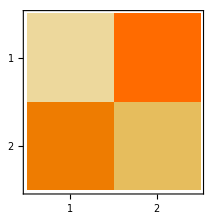

```mathematica
MatrixPlot[RandomInteger[20,{2,2}]]
```

```mathematica
MatrixForm[mat1  mat2] (* this is not matrix multiplication it is just corresponding element multiplication *)(* or we can use * in place of 'space' *)
```

(7 | 16 | 27
40 | 55 | 72)

```mathematica
MatrixForm[mat1+mat2]
```

(8 | 10 | 12
14 | 16 | 18)

```mathematica
MatrixForm[mat1/mat2]
```

(1/7 | 1/4 | 1/3
2/5 | 5/11 | 1/2)

## Referring to matrix rows and columns

```mathematica
mat={{7,14,21},{8,9,10}}
```

{{7,14,21},{8,9,10}}

```mathematica
MatrixForm[mat]
```

(7 | 14 | 21
8 | 9 | 10)

for referring value in 2D array(matrix ) we need row and column so we will provide two argument in mat[ [ i , j ] ] insted of 1 in array a [ [ i ] ]

```mathematica
mat[[1,2]] (* remember here we have 1 based indexing *)
```

14

for getting while row or column we use ‘All’ keyword

```mathematica
mat[[1,All]](* gives all columns for row 1 *)
```

{7,14,21}

```mathematica
mat[[All,2]]
```

{14,9}

similary as simple list we can also provide range of indexes instead of ‘All’ using  double semi colon ‘;;’ or Range[min,max] function

we can also provide list of index as list

```mathematica
mat[[1,1;;3]] (* same as simple list *)
```

{7,14,21}

```mathematica
mat[[1,Range[1,3]]]
```

{7,14,21}

```mathematica
mat[[1,{1,3}]]
```

{7,21}

we can also change value using the above method as we are using with lists

```mathematica
mat[[1,All]]=100;
```

```mathematica
MatrixForm[mat]
```

(100 | 100 | 100
8 | 9 | 10)

## Converting matrix to list

we can use Flatten[mat] method to convert matrix to list

this method flats row major.(row one by one)

```mathematica
mat={{1,2,3},{4,5,6}}
```

{{1,2,3},{4,5,6}}

```mathematica
Flatten[mat]
```

{1,2,3,4,5,6}

## Functions in Mathematica

## Creating a Function

syntax for defining a function is different from other languages here,
syntax is

```mathematica
<function_name>[<var_name>_,<var_name>_,..] := <expression_here>
```

underscore( _ ) is used after each variable name to show it is a argument variable.

example for making a function for mulitplying a number by 2

```mathematica
timestwo[x_] := x*2; (*definition *)
timestwo[10] (*calling*)
```

20

it is a good practice to not use Camel notation for user defined functions to that we never get conflict with already defined functions

pass by value mechanism is followed in mathematica and so a variable passed will not change its value until we take it in return

now if we pass some variable then its value value will not be changed until it is taken back reassigned.

```mathematica
x=10
```

10

```mathematica
timestwo[x]
```

20

```mathematica
x (* remain same as before *)
```

10

```mathematica
x=timestwo[x] (* for getting changed val
```

20

```mathematica
x
```

20

let us make a function for power

```mathematica
power[a_,b_]=a^b;
power[2,5]
```

32

## Clearing/Deleting a function

we can delete a function from its existence using Clear[fn_name] method same as variables.

```mathematica
Clear[power] (* removing power function from memory *)
```

```mathematica
power[2,5] (* now power[] is not availabe *)
```

power[2,5]

## Plotting in Mathematica

## Barchart

```mathematica
alist={4500,3000,2150,5879};
```

for making barchart from a data we have to use Barchart[list] keyword

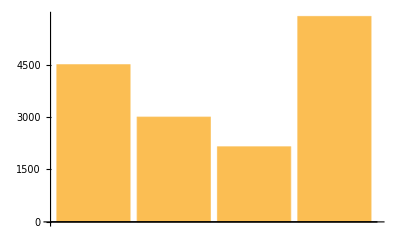

```mathematica
BarChart[alist]
```

BarChart3D[list] forms a 3D chart which we can roll

```mathematica
BarChart3D[alist]
```

-Graphics3D-

if we wanted to graph 2 or  series on a graph then we  can use a 2D list, where first row represents first value in all series and so on.

each series is of a different color, so in following example we have 3 series and 2 values for (similarly for Bar3D)

```mathematica
blist={{100,200,300},{400,500,600}}; (* here list={first_val_array,second_val_array,...} *)
```

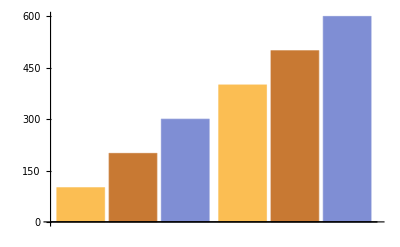

```mathematica
BarChart[blist]
```

## Histograms

histograms tell us the frequency of data, x-axis is value and y-axis is frequency.

while Barchart maps exactly value, Historgrams plots frequency of data.

```mathematica
alist={1,14,19,3,7,22,16,14}
```

{1,14,19,3,7,22,16,14}

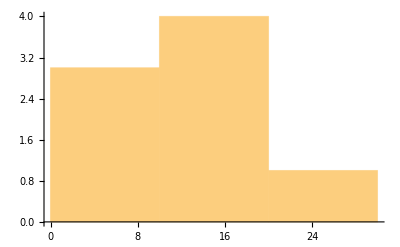

```mathematica
Histogram[alist]
```

one thing to that here 3 frequency if for [0..10) because 10 will be in next bucket.

## Scatter Plot

this is a simple plot which just plots some point in plan

ListPlot[list] and ListPlot3D[list] can be used

here list contains all points in xy plane(if two values for each point)
if only one is given it will be considered as y value and X value will be taken as 1,2,3,5,.... and so on.

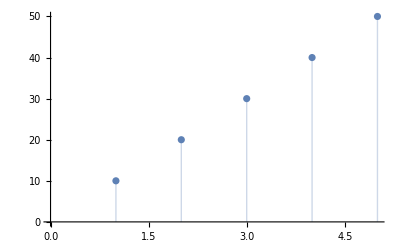

```mathematica
ListPlot[{10,20,30,40,50},Filling->Axis]
```

```mathematica
alist={{14,5},{7,7},{4,12},{11,6}}
```

```mathematica
{{14,5},{7,7},{14,12},{11,6}}
```

{{14,5},{7,7},{14,12},{11,6}}

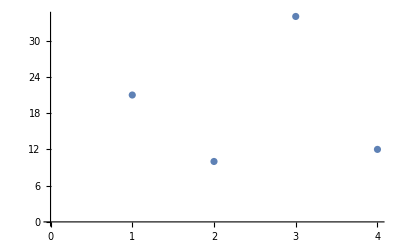

```mathematica
ListPlot[alist]
```

here size of points is very small so we can make them bigger using Properties, for this purpose we have ‘PointSize’ Property and inside this we will set size using PointSize[]

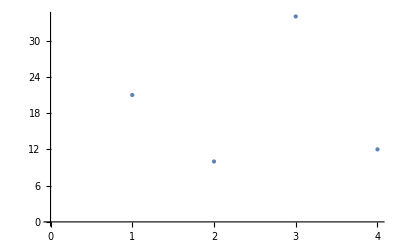

```mathematica
ListPlot[alist,PlotStyle->PointSize[Large]]
```

we can also have points in 3d space giving 3 values to each point, but for this we have to use ListPlot3D[list] method, if we give 2 values then x will be take as default(starting from 1)

```mathematica
blist={{14,5,12},{7,7,8},{4,12,4},{11,6,6}}
```

{{14,5,12},{7,7,8},{4,12,4},{11,6,6}}

```mathematica
ListPlot3D[blist]
```

-Graphics3D-

## List Line Plot

ListLinePlot[list] can be used to create a line plot insted of Point, it will join previous point to current for form line.

ListLinePlot[{y_1,y_2,…}] plots a line through a list of values, assumed to correspond to x coordinates 1, 2, … . 
ListLinePlot[{{x_1,y_1},{x_2,y_2},…}] plots a line through specific x and y positions. 
ListLinePlot[{list_1,list_2,…}] plots several lines.

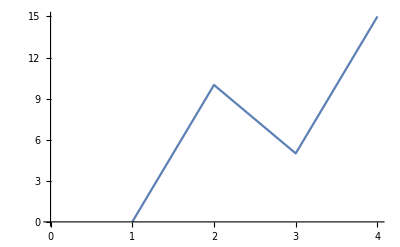

```mathematica
ListLinePlot[{0,10,5,15}](* if one dimension is given x will be taken by default starting from 1 *)
```

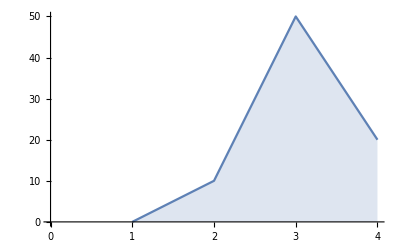

```mathematica
ListLinePlot[{0,10,50,20},Filling->Axis]
```

```mathematica
NOTE- for PairedBarChart see video and refrence
```

NOTE-and for PairedBarChart refrence see video

## Using Chart Options

we can set different types of properties for charts.

for using different color than default we can use ChartStyle property for all charts.(BarChart,Histogram)

for Plots(ListPlot,ListLinePlot,Plot) we can use PlotStyle

ChartStyle is an option for charting functions that specifies styles in which chart elements should be drawn.

```mathematica
alist={21,10,34,12}
```

{21,10,34,12}

```mathematica
Mean[alist]
```

77/4

### Coloring

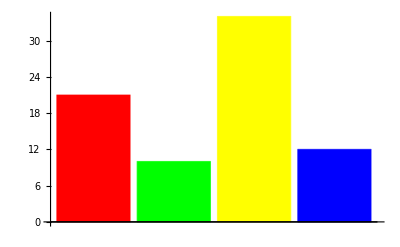

```mathematica
BarChart[alist,ChartStyle->{Red,Green,Yellow,Blue,Orange}]
```

if Colors are given then those colors will be used and Mathematica will not provide any colors, all colors will be provided cyclicly to all bars.it means if colors are less than bars then cyclically colors are proided.

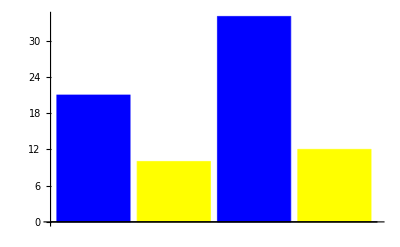

```mathematica
BarChart[alist,ChartStyle->{Blue,Yellow}]
```

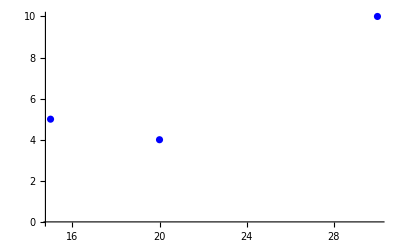

```mathematica
ListPlot[{{15,5},{20,4},{30,10}},PlotStyle->Blue] (* only one color can be used *)
```

### Plot Filling

for ListPlot[] we have property ‘Filling’

it doesnot have ChartStyle.

Filling is an option for ListPlot, Plot, Plot3D, and related functions that specifies what filling to add under points, curves, and surfaces.

Filling could be ‘Axis’, ‘Top’, ‘Bottom’, in Top axis comes from upperwards.

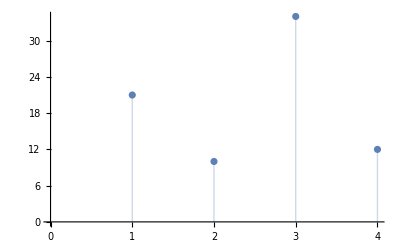

```mathematica
ListPlot[alist,Filling->Axis]
```

### Legends

legends can be used in all charts and plots

Lables used to tell about whole Plot or chart

#### Plot Legends and Labels

PlotLegends is an option for plot functions that specifies what legends to use.

PlotLabel is an option for graphics functions that specifies an overall label for a plot.

we can assign some string

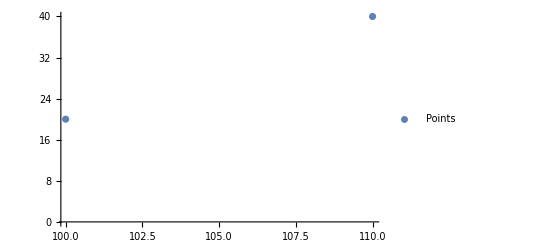

```mathematica
ListPlot[{{100,20},{110,40}},PlotLegends->{"Points"}]
```

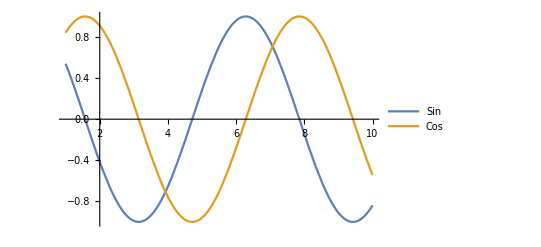

```mathematica
Plot[{Cos[x],Sin[x]},{x,1,10},PlotLegends->{"Sin","Cos","Tan"}] (* third is not there *)
```

‘Automatic’ will assign some numbers to them

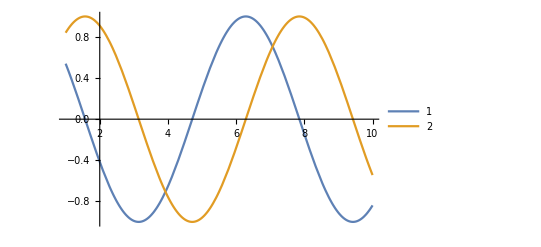

```mathematica
Plot[{Cos[x],Sin[x]},{x,1,10},PlotLegends->Automatic]
```

‘Expressions’ will automatically say the expression for that curve

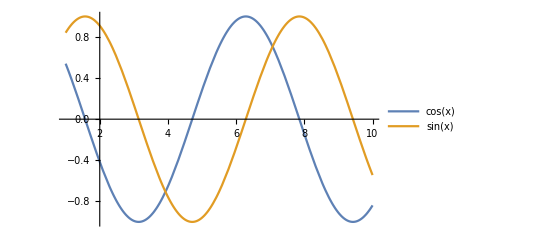

```mathematica
Plot[{Cos[x],Sin[x]},{x,1,10},PlotLegends->"Expressions"]
```

for Label we can provide Strings (for more see ref)

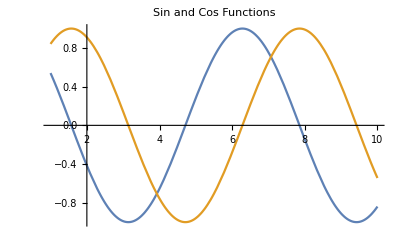

```mathematica
Plot[{Cos[x],Sin[x]},{x,1,10},PlotLabel->"Sin and Cos Functions"]
```

#### Chart Labels and Legends

chart legends are used for charts

only String can be used here

ChartLegends is an option for charting functions that specifies what legends should be used for chart elements.

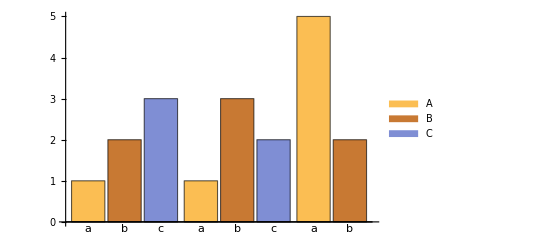

```mathematica
BarChart[{{1,2,3},{1,3,2},{5,2}},ChartLabels->{"a","b","c"},ChartLegends->{"A","B","C"}]
```

## Plotting Functions

Plot[] function can be used for this purpose

RowBox[{"Plot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{StyleBox["…", "TR"], ",", RowBox[{RowBox[{"{", StyleBox["x", "TI"], "}"}], "∈", StyleBox["reg", "TI"]}]}], "]"}] takes the variable StyleBox["x", "TI"] to be in the geometric region StyleBox["reg", "TI"].

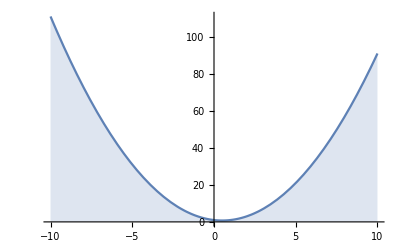

```mathematica
Plot[x^2-x+1,{x,-10,10},Filling->Bottom]
```

we can plot multiple functions givings list of expressions

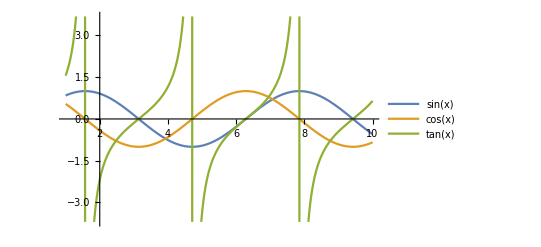

```mathematica
Plot[{Sin[x],Cos[x],Tan[x]},{x,1,10},PlotLegends->"Expressions"]
```

## Creating Interactive and Animated Visualizations

## Creating CDF file

cdf(computable document formate ) is made  for users who do not have whole mathematica, they could also see their content.

go to file>export>webembedded/standalone 
now you can choose to export entire document or only selected(if you have selected).

## Manipulationg input values for an expression

for manipulating values we use Manipulate[] function

RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a version of StyleBox["expr", "TI"] with controls added to allow interactive manipulation of the value of StyleBox["u", "TI"]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]], ",", StyleBox["du", "TI"]}], "}"}]}], "]"}] allows the value of StyleBox["u", "TI"] to vary between SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]] and SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]] in steps StyleBox["du", "TI"]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]]}], "}"}], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] takes the initial value of StyleBox["u", "TI"] to be SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["init", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["lbl", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] labels the controls for StyleBox["u", "TI"] with SubscriptBox[StyleBox["u", "TI"], StyleBox["lbl", "TI"]]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["u", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "}"}]}], "]"}] allows StyleBox["u", "TI"] to take on discrete values RowBox[{SubscriptBox[StyleBox["u", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] provides controls to manipulate each of the RowBox[{StyleBox["u", "TI"], ",", StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}]. 
RowBox[{"Manipulate", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{SubscriptBox[StyleBox["c", "TI"], StyleBox["u", "TI"]], "→", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], ",", RowBox[{SubscriptBox[StyleBox["c", "TI"], StyleBox["v", "TI"]], "→", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], ",", StyleBox["…", "TR"]}], "]"}] links the controls to the specified controllers on an external device.

```mathematica
Synta - Manipulate[expr,{u,umin,umax}]
now expression could be anything plot,graph,function etc.
```

example 1 - value for sin[x] function from 1 to 10

```mathematica
Manipulate[Sin[x],{x,1,10}]
```

```mathematica
Manipulate[Plot[Sin[x(1+a x)],{x,0,6}],{a,0,2}]
```

```mathematica
Manipulate[Plot[Sin[x+y],{x,0,10}],{y,0,10}]
```

here we can think of as we are manipulationg x of Sin[x] as  in Sin[x+y] , x needs to be given in 
Plot function so we can manipulate y.

```mathematica
Manipulate[Factor[x^n+1],{n,1,10,2}] (* here 2 is step *)
```

we can  manipulate many values at a time

```mathematica
Manipulate[Plot[x^3-a x^2+b,{x,-6,6}],{a,-15,25},{b,10,1000}]
```

## Animating Result in Mathematic

Animate[] is used for Animating  in mathematica

Animate[expr,{u,u_min,u_max}] generates an animation of expr in which u varies continuously from u_min to u_max. 
Animate[expr,{u,u_min,u_max,du}] takes u to vary in steps du. 
Animate[expr,{u,{u_1,u_2,…}}] makes u take on discrete values u_1, u_2, …. 
Animate[expr,{u,…},{v,…},…] varies all the variables u, v, ….

Animate[] is same as Manipulate[], although Manipulate have Animation embedded on it(on clicking plus(+) sign)

```mathematica
Animate[Plot[Cos[x+n],{x,1,20}],{n,1,10},AnimationRunning->False]
```

if we haven’t used AnimateRunning-> false then we get animate start running automatically , so if we wanted to run when only we click run button we use it.s

## Conditionals

## If statement

If[condition,on_true,on_false] evaluates condition and returns result according to condition.

If[condition,t,f] gives t if condition evaluates to True, and f if it evaluates to False. 
If[condition,t,f,u] gives u if condition evaluates to neither True nor False.

```mathematica
abs[x_]:=If[x<0,-x,x]
```

```mathematica
abs[1]
```

1

```mathematica
abs[0]
```

0

## Which Statement

return the value according to first true result

Which[test_1,value_1,test_2,value_2,…] evaluates each of the test_i in turn, returning the value of the value_i corresponding to the first one that yields True.

```mathematica
a=2;Which[a==1,x,a==2,b](* a=2; can be written on diffent line as well it is just delimiter *)
```

b

here in previous example a== 2 turns true so  b will be returned

## Looping Constructs

## Do

Do[expr,n] evaluates expr n times. 
Do[expr,{i,i_max}] evaluates expr with the variable i successively taking on the values 1 through i_max (in steps of 1). 
Do[expr,{i,i_min,i_max}] starts with i=i_min. 
Do[expr,{i,i_min,i_max,di}] uses steps di. 
Do[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Do[expr,{i,i_min,i_max},{j,j_min,j_max},…] evaluates expr looping over different values of j etc. for each i.

Example 1 - doing something  n times

```mathematica
Do[Print["hello"],{3}]
```

hello

hello

hello

Example 2 - Print the first four squares:

```mathematica
Do[Print[n^2],{n,4}] (* value of n will be taken from 1 to 4 *)
```

1

4

9

16

Example 3- n goes from - 3 to 5 in steps of 2 :

```mathematica
Do[Print[n],{n,-3,5,2}]
(* value of n will be from -3 to 5 in step=2 *)
```

-3

-1

1

3

5

## While

while evaluates until test fails

While[test,body] evaluates test, then body, repetitively, until test first fails to give True.

Example 1 - Print and increment n while the condition n<4 is satisfied:

```mathematica
n=1;
While[n<4,Print[n];n++]
```

1

2

3

```mathematica
(* here n<4 is test and remaining is body. *)
```

post and pre increment works same as c/c++

```mathematica
n=1;While[n++<4,Print[n]](* post increment *)
```

2

3

4

```mathematica
n=1;While[++n<4,Print[n]] (* pre increment *)
```

2

3

## For

same as c/c++, it has 4 things intialise,test,increment,body

For[start,test,incr,body] executes start, then repeatedly evaluates body and incr until test fails to give True.

example 1- Printing from 1 to 5

```mathematica
For[i=1,i≤5,i++,Print[i]]
```

1

2

3

4

5

comma ends a part of For[] (applicable to all functions), and semicolon(;) ends one statement , so we can have multiple semicolon separated statements in a part.

Example

```mathematica
For[i=1;t=x,i<4,i++,t=i+t^2;Print[t]]
```

1+x^2

2+(1+x^2)^2

3+(2+(1+x^2)^2)^2

```mathematica
(* here we have intialise i=1 and t=x and we are going until i<4 *)
```

## Break and Continue

Break[] breaks the nearest loop (same as c/c++)

Break[] exits the nearest enclosing Do, For, or While.

```mathematica
For[i=1,i<1000,i++,If[i>10,Break[]]];Print[i] (* show i after For ends *)
```

11

Break[] never passes any argument to itself

Continue[] continues loop without executing rest of the body(same as c/c++)

Continue[] exits to the nearest enclosing Do, For, or While in a procedural program.

```mathematica
Do[If[!PrimeQ[i],Continue[]];Print[i],{i,10}]
```

2

3

5

7

## Table in Mathematica

Table is used to generate different types of list of values.

Table[expr,n] generates a list of n copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

Table always have two parts expression and iterator.
iterator defines how many times the expression needs to be put in Table.

Example 1- having a list of 9 “hello”

```mathematica
Table["hello",9]
```

{hello,hello,hello,hello,hello,hello,hello,hello,hello}

Example 2- having list of squares of number 1 to 10

```mathematica
Table[n^2,{n,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

as 1 is by default imin we can use

```mathematica
Table[n^2,{n,10}]
```

{1,4,9,16,25,36,49,64,81,100}

Example 3 - Make a 4×3 matrix:

```mathematica
MatrixForm[Table[i+j,{i,1,5},{j,1,5}]]
```

(2 | 3 | 4 | 5 | 6
3 | 4 | 5 | 6 | 7
4 | 5 | 6 | 7 | 8
5 | 6 | 7 | 8 | 9
6 | 7 | 8 | 9 | 10)

Table is most commonly used for Plotting

Example 4 - plot primes first 50 Primes

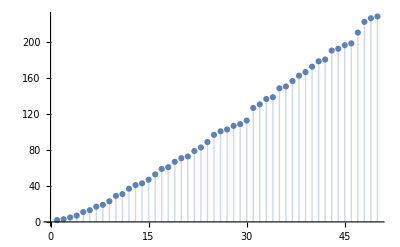

```mathematica
ListPlot[Table[Prime[i],{i,1,50}],Filling->Bottom]
```